Reading csv file with commands

```mathematica
data= Import["D:/avg.csv"]
Plot[data,1:100]
```

{{Rep,Proportion},{1,0.581515},{2,0.583249},{3,0.583451},{4,0.583151},{5,0.5823},{6,0.583352},{7,0.58165},{8,0.582354},{9,0.583306},{10,0.581853},{11,0.582904},{12,0.581313},{13,0.581151},{14,0.582215},{15,0.584746},{16,0.581575},{17,0.582377},{18,0.581412},{19,0.583932},{20,0.582334},{21,0.582222},{22,0.583677},{23,0.58185},{24,0.582077},{25,0.582866},{26,0.582361},{27,0.585184},{28,0.581574},{29,0.583651},{30,0.582911},{31,0.583347},{32,0.58315},{33,0.58275},{34,0.584919},{35,0.583446},{36,0.582537},{37,0.582347},{38,0.58308},{39,0.584121},{40,0.584014},{41,0.581509},{42,0.582248},{43,0.583901},{44,0.581674},{45,0.582997},{46,0.583238},{47,0.582804},{48,0.581878},{49,0.583721},{50,0.581982},{51,0.58384},{52,0.583281},{53,0.581884},{54,0.582551},{55,0.582406},{56,0.580822},{57,0.581821},{58,0.582993},{59,0.582786},{60,0.583656},{61,0.581761},{62,0.58287},{63,0.581337},{64,0.583347},{65,0.58144},{66,0.583292},{67,0.582664},{68,0.582594},{69,0.583142},{70,0.582268},{71,0.583931},{72,0.581954},{73,0.58237},{74,0.580132},{75,0.584605},{76,0.583568},{77,0.583616},{78,0.582358},{79,0.581879},{80,0.584264},{81,0.582195},{82,0.583293},{83,0.58279},{84,0.58227},{85,0.584933},{86,0.582513},{87,0.579442},{88,0.58384},{89,0.581014},{90,0.583077},{91,0.58349},{92,0.583389},{93,0.583222},{94,0.581005},{95,0.581851},{96,0.582991},{97,0.583746},{98,0.582364},{99,0.583171},{100,0.582752}}

```mathematica
{{0.581514532,0.583249402,0.583451428,0.583151376,0.58230005,0.583352104,0.581649697,0.582354079,0.583305847,0.581853431,0.582904306,0.581313436,0.581151189,0.582214651,0.584745516,0.581575061,0.582377057,0.581411727,0.583932476,0.582334095,0.582222242,0.583677442,0.581849658,0.582076799,0.582866091,0.582361273,0.585183546,0.58157447,0.583651419,0.582911254,0.583347296,0.583149937,0.582749667,0.584919319,0.583446227,0.582537342,0.582347425,0.583079744,0.584121071,0.584014306,0.581508742,0.582247856,0.5839011,0.581673671,0.582997172,0.583238315,0.582803888,0.581877724,0.583721478,0.581982221,0.583840379,0.583280742,0.581884294,0.582550736,0.582406333,0.580821873,0.581821034,0.582992546,0.582785721,0.583656376,0.581761334,0.582869688,0.581336705,0.583346967,0.581439718,0.583291997,0.582663637,0.582594262,0.583141675,0.582267897,0.583930525,0.581954216,0.582370387,0.580132488,0.584604771,0.583568145,0.583616265,0.582358109,0.581878667,0.584264374,0.582195119,0.583292969,0.582790426,0.582270209,0.58493286,0.58251318,0.579441738,0.583839792,0.581013977,0.583077391,0.583490048,0.583388804,0.583221693,0.58100495,0.581851094,0.582990814,0.583745617,0.582364066,0.583171364,0.58275197}}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{0.581515,0.583249,0.583451,0.583151,0.5823,0.583352,0.58165,0.582354,0.583306,0.581853,0.582904,0.581313,0.581151,0.582215,0.584746,0.581575,0.582377,0.581412,0.583932,0.582334,0.582222,0.583677,0.58185,0.582077,0.582866,0.582361,0.585184,0.581574,0.583651,0.582911,0.583347,0.58315,0.58275,0.584919,0.583446,0.582537,0.582347,0.58308,0.584121,0.584014,0.581509,0.582248,0.583901,0.581674,0.582997,0.583238,0.582804,0.581878,0.583721,0.581982,0.58384,0.583281,0.581884,0.582551,0.582406,0.580822,0.581821,0.582993,0.582786,0.583656,0.581761,0.58287,0.581337,0.583347,0.58144,0.583292,0.582664,0.582594,0.583142,0.582268,0.583931,0.581954,0.58237,0.580132,0.584605,0.583568,0.583616,0.582358,0.581879,0.584264,0.582195,0.583293,0.58279,0.58227,0.584933,0.582513,0.579442,0.58384,0.581014,0.583077,0.58349,0.583389,0.583222,0.581005,0.581851,0.582991,0.583746,0.582364,0.583171,0.582752}}

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{0.581515,0.583249,0.583451,0.583151,0.5823,0.583352,0.58165,0.582354,0.583306,0.581853,0.582904,0.581313,0.581151,0.582215,0.584746,0.581575,0.582377,0.581412,0.583932,0.582334,0.582222,0.583677,0.58185,0.582077,0.582866,0.582361,0.585184,0.581574,0.583651,0.582911,0.583347,0.58315,0.58275,0.584919,0.583446,0.582537,0.582347,0.58308,0.584121,0.584014,0.581509,0.582248,0.583901,0.581674,0.582997,0.583238,0.582804,0.581878,0.583721,0.581982,0.58384,0.583281,0.581884,0.582551,0.582406,0.580822,0.581821,0.582993,0.582786,0.583656,0.581761,0.58287,0.581337,0.583347,0.58144,0.583292,0.582664,0.582594,0.583142,0.582268,0.583931,0.581954,0.58237,0.580132,0.584605,0.583568,0.583616,0.582358,0.581879,0.584264,0.582195,0.583293,0.58279,0.58227,0.584933,0.582513,0.579442,0.58384,0.581014,0.583077,0.58349,0.583389,0.583222,0.581005,0.581851,0.582991,0.583746,0.582364,0.583171,0.582752}}[1]

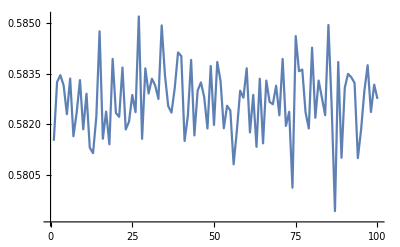

```mathematica
d1 = ListLinePlot[data]
```

```mathematica
Show[d1,Method->{"OptimizePlotMarkers"->True,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

-Graphics-

```mathematica
d1 = ListLinePlot[data]
```

-Graphics-

```mathematica
data
```

{{Rep,Proportion},{1,0.581515},{2,0.583249},{3,0.583451},{4,0.583151},{5,0.5823},{6,0.583352},{7,0.58165},{8,0.582354},{9,0.583306},{10,0.581853},{11,0.582904},{12,0.581313},{13,0.581151},{14,0.582215},{15,0.584746},{16,0.581575},{17,0.582377},{18,0.581412},{19,0.583932},{20,0.582334},{21,0.582222},{22,0.583677},{23,0.58185},{24,0.582077},{25,0.582866},{26,0.582361},{27,0.585184},{28,0.581574},{29,0.583651},{30,0.582911},{31,0.583347},{32,0.58315},{33,0.58275},{34,0.584919},{35,0.583446},{36,0.582537},{37,0.582347},{38,0.58308},{39,0.584121},{40,0.584014},{41,0.581509},{42,0.582248},{43,0.583901},{44,0.581674},{45,0.582997},{46,0.583238},{47,0.582804},{48,0.581878},{49,0.583721},{50,0.581982},{51,0.58384},{52,0.583281},{53,0.581884},{54,0.582551},{55,0.582406},{56,0.580822},{57,0.581821},{58,0.582993},{59,0.582786},{60,0.583656},{61,0.581761},{62,0.58287},{63,0.581337},{64,0.583347},{65,0.58144},{66,0.583292},{67,0.582664},{68,0.582594},{69,0.583142},{70,0.582268},{71,0.583931},{72,0.581954},{73,0.58237},{74,0.580132},{75,0.584605},{76,0.583568},{77,0.583616},{78,0.582358},{79,0.581879},{80,0.584264},{81,0.582195},{82,0.583293},{83,0.58279},{84,0.58227},{85,0.584933},{86,0.582513},{87,0.579442},{88,0.58384},{89,0.581014},{90,0.583077},{91,0.58349},{92,0.583389},{93,0.583222},{94,0.581005},{95,0.581851},{96,0.582991},{97,0.583746},{98,0.582364},{99,0.583171},{100,0.582752}}

```mathematica
Transpose[%52]
```

{{Rep,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{Proportion,0.581515,0.583249,0.583451,0.583151,0.5823,0.583352,0.58165,0.582354,0.583306,0.581853,0.582904,0.581313,0.581151,0.582215,0.584746,0.581575,0.582377,0.581412,0.583932,0.582334,0.582222,0.583677,0.58185,0.582077,0.582866,0.582361,0.585184,0.581574,0.583651,0.582911,0.583347,0.58315,0.58275,0.584919,0.583446,0.582537,0.582347,0.58308,0.584121,0.584014,0.581509,0.582248,0.583901,0.581674,0.582997,0.583238,0.582804,0.581878,0.583721,0.581982,0.58384,0.583281,0.581884,0.582551,0.582406,0.580822,0.581821,0.582993,0.582786,0.583656,0.581761,0.58287,0.581337,0.583347,0.58144,0.583292,0.582664,0.582594,0.583142,0.582268,0.583931,0.581954,0.58237,0.580132,0.584605,0.583568,0.583616,0.582358,0.581879,0.584264,0.582195,0.583293,0.58279,0.58227,0.584933,0.582513,0.579442,0.58384,0.581014,0.583077,0.58349,0.583389,0.583222,0.581005,0.581851,0.582991,0.583746,0.582364,0.583171,0.582752}}

```mathematica
Plot[Transpose[%52],{x,0,10},PlotRange->Automatic]
```

-Graphics-

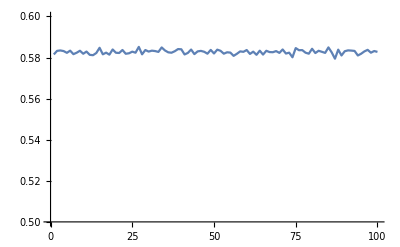

```mathematica
p1 = ListLinePlot[data, PlotRange->{{1,1}{0.5,0.6}}]
```

```mathematica
Export["C:\\Users\\gg\\Documents\\average pt plot.jpg",%76,"JPEG"]
```

C:\Users\gg\Documents\average pt plot.jpg

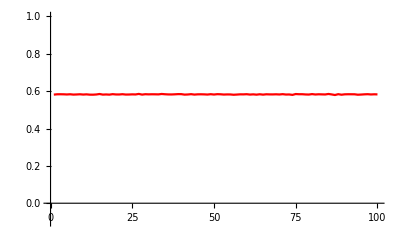

```mathematica
p2 = ListLinePlot[data,PlotStyle->{Red,.03}, PlotRange->{{-1,1}{0.1,1}}]
```

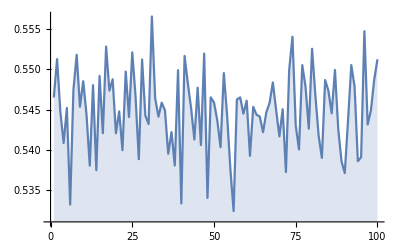

```mathematica
StackedListPlot[data]
```

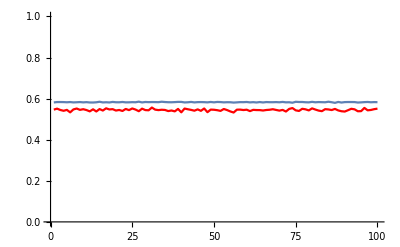

```mathematica
Show[p1,p2]
```

```mathematica
Show[%114,AxesLabel->{HoldForm[tick],None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%114,AxesLabel->{HoldForm[tick],None},PlotLabel->HoldForm[Simulations:Average proportion of public transport strategists],LabelStyle->{GrayLevel[0]}]
```

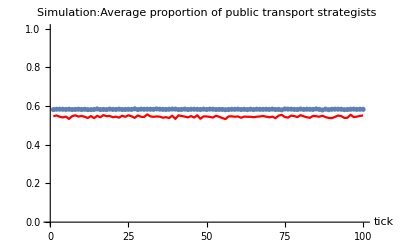

```mathematica
Show[%107,AxesLabel->{HoldForm[tick],None},PlotLabel->HoldForm[Simulation:Average proportion of public transport strategists],LabelStyle->{GrayLevel[0]}]
```

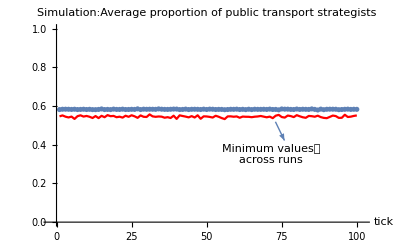

```mathematica
Export["C:\\Users\\gg\\Documents\\average prop avgmin.png",%108,"PNG"]
```

C:\Users\gg\Documents\average prop avgmin.png

```mathematica
data2= Import["D:/avg2.csv"]
```

{{Rep,Proportion},{1,0.456528},{2,0.443249},{3,0.452003},{4,0.465554},{5,0.460215},{6,0.461414},{7,0.452541},{8,0.448211},{9,0.458311},{10,0.451734},{11,0.459387},{12,0.456405},{13,0.458558},{14,0.449825},{15,0.457481},{16,0.457604},{17,0.454619},{18,0.464872},{19,0.45347},{20,0.465323},{21,0.451197},{22,0.452419},{23,0.450659},{24,0.45039},{25,0.458288},{26,0.454399},{27,0.450659},{28,0.454301},{29,0.448628},{30,0.457896},{31,0.448842},{32,0.45347},{33,0.453641},{34,0.458827},{35,0.454937},{36,0.45858},{37,0.456674},{38,0.460463},{39,0.452663},{40,0.445102},{41,0.453054},{42,0.463815},{43,0.467599},{44,0.455059},{45,0.456528},{46,0.454276},{47,0.461828},{48,0.449314},{49,0.447552},{50,0.453323},{51,0.458457},{52,0.454521},{53,0.462345},{54,0.45078},{55,0.46042},{56,0.46214},{57,0.457089},{58,0.452688},{59,0.457335},{60,0.460856},{61,0.45951},{62,0.449139},{63,0.467043},{64,0.459634},{65,0.456843},{66,0.462883},{67,0.457504},{68,0.445968},{69,0.45457},{70,0.449287},{71,0.45078},{72,0.455499},{73,0.456013},{74,0.456452},{75,0.450928},{76,0.46371},{77,0.449973},{78,0.455914},{79,0.450242},{80,0.452932},{81,0.459656},{82,0.454937},{83,0.453739},{84,0.461538},{85,0.459903},{86,0.456551},{87,0.459823},{88,0.448387},{89,0.461787},{90,0.461538},{91,0.466218},{92,0.470667},{93,0.460194},{94,0.452125},{95,0.451856},{96,0.448749},{97,0.454839},{98,0.450121},{99,0.457358},{100,0.455376}}

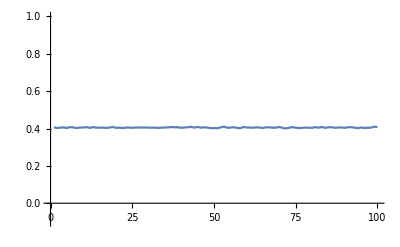

```mathematica
d1 = ListLinePlot[data2, PlotRange->{{-1,1}{0.1,1}}]
```

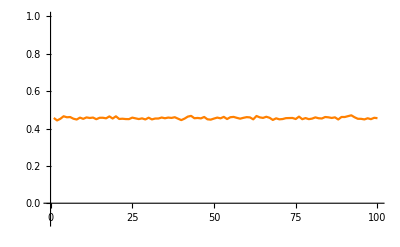

```mathematica
d2 = ListLinePlot[data2,PlotStyle->{Orange,.6}, PlotRange->{{-1,1}{0.1,1}}]
```

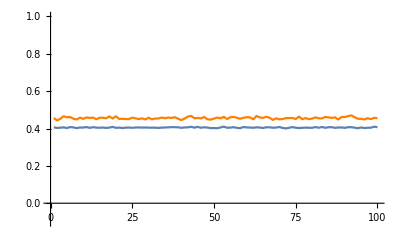

```mathematica
Show[d1,d2]
```

```mathematica
Show[%167,AxesLabel->{HoldForm[tick],None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```